# Ensemble Bcd Binding Calculations

## Case 1: 4 state non-cooperative chain

```mathematica
Clear["Global`*"]
```

```mathematica
Q = {{-3*kon,koff,0,0},{3*kon,-2*kon-koff,2*koff,0},{0,2*kon,-kon-2*koff,3*koff},{0,0,kon,-3*koff}};
```

```mathematica
MatrixForm[Q]
```

(-3 kon | koff | 0 | 0
3 kon | -koff-2 kon | 2 koff | 0
0 | 2 kon | -2 koff-kon | 3 koff
0 | 0 | kon | -3 koff)

```mathematica
Total[Q]
```

{0,0,0,0}

#### Calculate Steady-state vector (equal to first eigenvector divided by normalization factor)

```mathematica
eigVectors = Eigenvectors[Q];
```

```mathematica
ssVec = FullSimplify[eigVectors[[1]] / Total[eigVectors[[1]]]];
```

```mathematica
pdRate = ssVec[[4]]+ ssVec[[3]]
```

(3 koff kon^2)/(koff+kon)^3+kon^3/(koff+kon)^3

### Calculate first passage time for 2->3

```mathematica
eqET23 = ET23 == FullSimplify[-1/Q[[2,2]]*(1 +Q[[1,2]]*ET13)]
```

ET23==(1+ET13 koff)/(koff+2 kon)

```mathematica
eqET13 = ET13 == -1/Q[[1,1]]+ET23
```

ET13==ET23+1/(3 kon)

```mathematica
solET23=Solve[{eqET23,eqET13},{ET23,ET13}]
```

{{ET23→-(-koff-3 kon)/(6 kon^2),ET13→-(-koff-5 kon)/(6 kon^2)}}

```mathematica
ET23exp = FullSimplify[ET23/.solET23[[1]]]
```

(koff+3 kon)/(6 kon^2)

```mathematica
konEff[kon_] = 1/ET23exp /. koff->1
```

(6 kon^2)/(1+3 kon)

```mathematica
konEff[10]
```

600/31

#### Calculate first passage time for 3->2

```mathematica
eqET32 = ET32 == -1/Q[[3,3]]*(1 +Q[[4,3]]*ET42)
```

ET32==-(1+ET42 kon)/(-2 koff-kon)

```mathematica
eqET42 = ET42 == -1/Q[[4,4]]+ET32
```

ET42==ET32+1/(3 koff)

```mathematica
solET32=Solve[{eqET32,eqET42},{ET32,ET42}]
```

{{ET32→-(-3 koff-kon)/(6 koff^2),ET42→-(-5 koff-kon)/(6 koff^2)}}

```mathematica
ET32exp = FullSimplify[ET32/.solET32[[1]]]
```

(3 koff+kon)/(6 koff^2)

```mathematica
koffEff[kon_] = 1/ET32exp
```

(6 koff^2)/(3 koff+kon)

```mathematica
koffEff[10]
```

6/13

```mathematica
FullSimplify[(ssVec[[3]]/ (ssVec[[3]] + ssVec[[4]]))*koff]
```

(3 koff^2)/(3 koff+kon)

## Plot range of possible effective on/off rates for different molecular kon’s

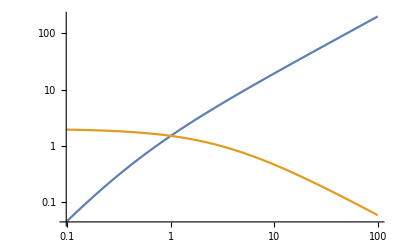

```mathematica
LogLogPlot[{konEff [kon],koffEff [kon]},{kon,0,100}]
```

So it’s clear that this simple, non-cooperative model cannot produce slow off/on dynamics

## Case 2: 4 state cooperative chain

Let’s assume quadratic cooperativity

```mathematica
Q2 = {{-kon,koff,0,0},{kon,-kon-koff,2*koff,0},{0,kon,-n*kon-2*koff,3*koff},{0,0,n*kon,-3*koff}};
```

```mathematica
MatrixForm[Q2]
```

(-kon | koff | 0 | 0
kon | -koff-kon | 2 koff | 0
0 | kon | -2 koff-kon n | 3 koff
0 | 0 | kon n | -3 koff)

```mathematica
Total[Q2]
```

{0,0,0,0}

#### Calculate Steady-state vector (equal to first eigenvector divided by normalization factor)

```mathematica
eigVectors2 = Eigenvectors[Q2];
```

```mathematica
ssVec2 = FullSimplify[eigVectors2[[1]] / Total[eigVectors2[[1]]]];
```

```mathematica
pdRate = ssVec[[4]]+ ssVec[[3]]
```

(3 koff kon^2)/(koff+kon)^3+kon^3/(koff+kon)^3

### Calculate first passage time for 2->3

```mathematica
eq2ET23 = ET23 == FullSimplify[-1/Q2[[2,2]]*(1 +Q2[[1,2]]*ET13)]
```

ET23==(1+ET13 koff)/(koff+kon)

```mathematica
eq2ET13 = ET13 == -1/Q2[[1,1]]+ET23
```

ET13==ET23+1/kon

```mathematica
sol2ET23=Solve[{eq2ET23,eq2ET13},{ET23,ET13}]
```

{{ET23→-(-koff-kon)/kon^2,ET13→-(-koff-2 kon)/kon^2}}

```mathematica
ET23exp2 = FullSimplify[ET23/.sol2ET23[[1]]]
```

(koff+kon)/kon^2

```mathematica
konEff2= 1/ET23exp2/. {koff->1}
```

kon^2/(1+kon)

```mathematica
konEff[10]
```

600/31

#### Calculate first passage time for 3->2

```mathematica
eq2ET32 = ET32 == -1/Q2[[3,3]]*(1 +Q2[[4,3]]*ET42)
```

ET32==-(1+ET42 kon n)/(-2 koff-kon n)

```mathematica
eq2ET42 = ET42 == -1/Q2[[4,4]]+ET32
```

ET42==ET32+1/(3 koff)

```mathematica
sol2ET32=Solve[{eq2ET32,eq2ET42},{ET32,ET42}]
```

{{ET32→-(-3 koff-kon n)/(6 koff^2),ET42→-(-5 koff-kon n)/(6 koff^2)}}

```mathematica
ET32exp2= FullSimplify[ET32/.sol2ET32[[1]]]
```

(3 koff+kon n)/(6 koff^2)

```mathematica
koffEff2 = 1/ET32exp2/. {koff->1}
```

6/(3+kon n)

```mathematica
koffEff[10]
```

6/13

## Plot range of possible effective on/off rates for different molecular kon’s

```mathematica
randVals= Table[{ kon->  10^RandomReal[{-2,2}],n->  10^RandomReal[{-5,5}]}, {100000}];
```

```mathematica
nkonSweep = Table[{konEff2/.randVals[[i]], koffEff2/.randVals[[i]]}, {i,1,Length[randVals]}];
```

```mathematica
nkonSweep[[101]]
```

{73.88,0.3348}

```mathematica
koffEff2/.{kon->5,n->10}
```

6/53

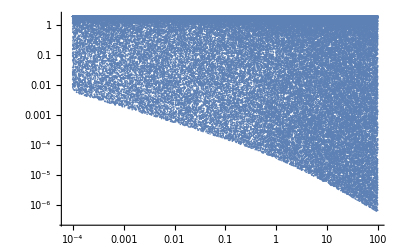

```mathematica
ListLogLogPlot[nkonSweep, PlotRange->All]
```